```mathematica
(*Friday Topological Physics (tunable version) *)
Clear["Global`*"];
htEigenSys[t0_,numOfatoms0_,ϵ0_]:=Module[
{t=t0,numOfatoms=numOfatoms0,ϵ=ϵ0,Ht,bound1,bound2},(*number of atoms on the 1-dim chain*)
bound1={{1,3}->-t,{2,4}->t,{1,4}->t};(*boundary condition 1*)
bound2={{2numOfatoms-1,2numOfatoms-2}->-t,{2numOfatoms,2numOfatoms}->0};(*boundary condition 2*)
Ht=SparseArray@({bound1,Table[{
{2i-1,2i+1}->-t,
{2i,2i+2}->t,
{2i-1,2i+2}->t,
{2i-1,2i-2}->-t},{i,2,numOfatoms-1}],bound2}//Flatten);(*i denotes number of the atom, odd num denote s orbital, even num denote p orbital*)
Ht+=(Ht//ConjugateTranspose);
Ht=-Normal@Ht+ϵ DiagonalMatrix@(Table[{1,-1},numOfatoms]//Flatten);(*normal form to boost calculation when matrix becomes large*)
ListLinePlot[Drop[(Eigensystem[N@Ht])[[2,-1]]^2,{2,2numOfatoms,2}]]
]
(*do not put more than 10^4 atoms in the chain*)
```

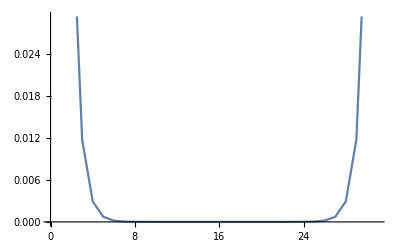

```mathematica
htEigenSys[1,31,1]
```